# Lista 3 - Arthur Silva Magalhães

## NUSP - 12629595

## 1.

Primeiramente vamos definir as equações de movimento dos dois corpos no sistema físico apresentado.

Considerando que ω1^2= k/m1 e ω2^2= k/m2, podemos definir as equações diferenciais de movimento para x1(t) e x2(t) da seguinte forma:

```mathematica
eqx1 = x1''[t] - ω1^2*(x2[t] - 2*x1[t])==0;
eqx2 = x2''[t] - ω2^2*(x1[t] - x2[t])==0;
```

Agora vamos obter as soluções para estas equações diferenciais, utilizando as condições iniciais fornecidas pela questão.

```mathematica
sol= DSolve[{eqx1, eqx2,x1'[0]==0,x2'[0]==0, x1[0]== 0, x2[0]==A},{x1[t],x2[t]},t]//FullSimplify//First; (* O FullSimplify foi inserido para termos uma forma mais compacta das soluções, e o First foi inserido para eliminarmos as chaves a mais da lista formada e conseguirmos trabalhar com cada um dos seus componentes futuramente *)
```

Para cada solução fornecida vamos associar a uma função de posição  x1(t) e x2(t) respectivamente:

```mathematica
posx1[t_] := x1[t]/.sol[[1]]
posx2[t_] := x2[t]/.sol[[2]]
```

Agora vamos tratar cada caso pedido pela questão para diferentes combinações de frequência.

ω1 = ω2 :

```mathematica
optam={ImageSize->Large,LabelStyle->Large}; (* Um conjunto de parâmetros visuais a serem usados para a plotagem de todos os gráficos *)
```

Primeiro vamos fazer o caso de frequências iguais, escolhemos ω2 = ω1 =5

```mathematica
subs1 = {ω1 ->5, ω2->5,A->2};
```

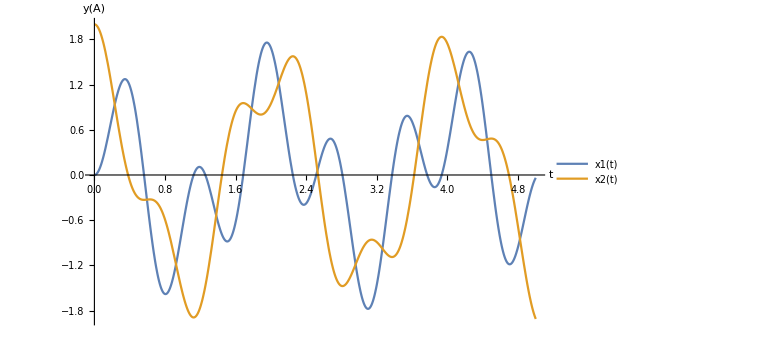

```mathematica
Plot[Evaluate[{posx1[t],posx2[t]}/.subs1],{t,0,5},AxesLabel->{"t","y(A)"},Evaluate[optam],PlotLegends->{"x1(t)","x2(t)"}]
```

Podemos perceber que as duas massa estão oscilando de forma não periódica, no entanto nenhuma se mostra com muito mais oscilações que outra em um mesmo intervalo de tempo, uma vez que por terem frequências iguais também tem massas iguais (vide nossa definição de ω anteriormente), e como por  definição do exercício ambas molas tem a mesma constante elástica κ, é de se esperar um movimento semelhante entre os corpos.

### ω1 << ω2:

Agora vamos analisar o caso em que ω2 é muito maior que ω1. Para isso foram escolhidos os valores de 25 e 1 respectivamente.

```mathematica
subs2 = {ω1 ->1, ω2->25,A->2};
```

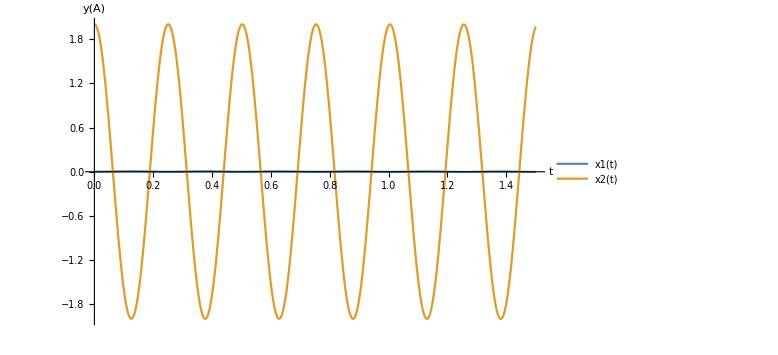

```mathematica
Plot[Evaluate[{posx1[t],posx2[t]}/.subs2],{t,0,1.5},AxesLabel->{"t","y(A)"},Evaluate[optam],PlotLegends->{"x1(t)","x2(t)"}]
```

Para entendermos fisicamente este resultado, devemos analisar o que significa ω2 ser muito maior que ω1 e quais consequências isso trás para o sistema. Se voltarmos para a definição de ω2, podemos ver que ter uma frequência grande acarreta em ter uma massa muito pequena (uma vez que as constantes elásticas das molas são um fator comum e  a massa e a frequência são inversamente proporcionais). Utilizando-se do mesmo pensamento, podemos inferir que ω1 é muito pequeno pois m1 é uma massa muito maior que a m2. Temos então:  ω1 << ω2  , m1 >> m2.

Pensando desta forma, podemos imaginar que m1 é tão maior que se comportar como um corpo sólido, quase que imóvel, como se fosse uma parede.Assim é como se m2 estivesse oscilando de maneira periódica e sem atrito em um sistema simples de massa mola, como vemos no gráfico.

#### ω1 >> ω2:

```mathematica
subs3 = {ω1 ->25, ω2->1,A->2};
```

Agora vamos analisar o caso em que ω1 >> ω2.Para isso foram escolhidos os valores de 25 e 1 respectivamente.

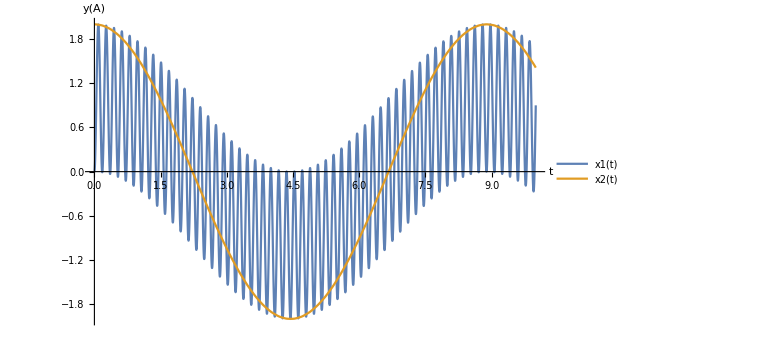

```mathematica
Plot[Evaluate[{posx1[t],posx2[t]}/.subs3],{t,0,10},AxesLabel->{"t","y(A)"},Evaluate[optam],PlotLegends->{"x1(t)","x2(t)"},PlotPoints->200]
```

Podemos fazer  a análise física deste sistema de maneira análoga ao do sistema anterior, no entanto agora as implicações no sistema serão diferentes. Neste caso podemos considerar que a massa m2 é muito maior que a m1, isso é visto claramente no gráfico quando vemos que m1 realiza muitas oscilações quando comparada com m2. No entanto, diferentemente do caso anterior, agora o sistema não se comporta mais como um massa mola simples, pois m1 está sujeito a forças restaurativas de 2 molas e uma destas molas está diretamente associada a massa m2. Isso faz com que m1 oscile de maneira muito rápida, enquanto m2 vagarosamente realiza suas oscilações, levando a massa m1 a oscilar cada vez mais em  A < 0 quando x2 é < 0 e em A >0 quando x2 > 0.

#### ω1 = ω2 = A = 1

Vamos fixar agora todos os parâmetros livres como 1.

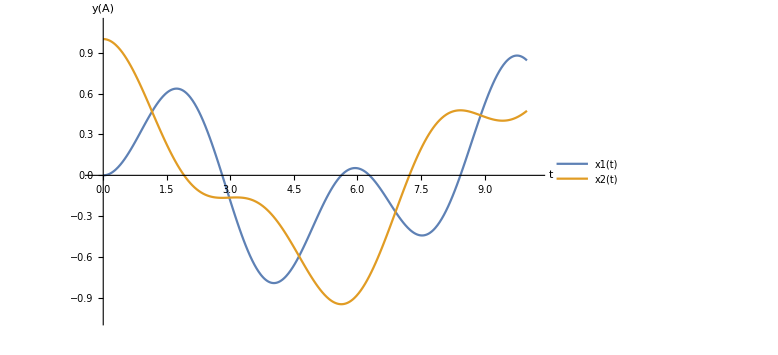

```mathematica
subs4 = {ω1 ->1, ω2->1,A->1};
Plot[Evaluate[{posx1[t],posx2[t]}/.subs4],{t,0,10},AxesLabel->{"t","y(A)"},Evaluate[optam],PlotLegends->{"x1(t)","x2(t)"},PlotPoints->200]
```

Podemos ver exatamente no gráfico os pontos de intersecção entre x1 e x2.  O interessante destes pontos é que neles a mola da direita não contém energia potencial. Podemos imaginar isto como se pegássemos exatamente o momento em que x1 = x2, neste momento podemos dizer com certeza que a mola da direita não estará nem contraída e nem estendida, uma vez que ela  depende da diferença entre os deslocamentos até o ponto de equilíbrio das duas massas. No entanto a mola 1 depende, de forma direta, exclusivamente do deslocamento da massa 1.

Para encontrar de forma exata estes pontos utilizei uma função que calculasse a raiz para x1 = x2, e forneci um pequeno chute baseado em uma análise visual do gráfico mostrado.

```mathematica
intersec1 = FindRoot[posx1[t] == posx2[t] /. subs4,{t,1}]
intersec2 = FindRoot[posx1[t] == posx2[t] /. subs4,{t,3}]
intersec3 = FindRoot[posx1[t] == posx2[t] /. subs4,{t,4.5}]
intersec4 = FindRoot[posx1[t] == posx2[t] /. subs4,{t,7}]
```

{t→1.15211}

{t→2.975}

{t→4.62207}

{t→6.89855}

## 2.

Primeiramente  vamos organizar os dados da tabela em uma lista em que cada componente é a Tupla de pares ordenados da forma (x,y), em que x é a Temperatura T e y são os valores de tensão superficial σ.

```mathematica
dados = {{-8,77.0},{-5,76.4},{0,75.6},{5,74.9},{10,74.22},{15,73.49},{18,73.05},{20,72.75},{30,71.18},{40,69.56},{50,67.91},{60,66.18}, {70,64.4}, {80,62.6},{100,58.9}};
optam={ImageSize->Large,LabelStyle->Large};
```

Agora vamos plotar um gráfico com os valores experimentais da tabela para ter uma noção melhor de como estes pontos se comportam.

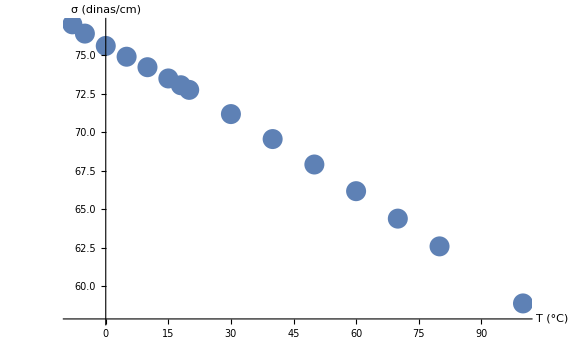

```mathematica
grafico1a=ListPlot[dados,PlotStyle->PointSize[0.025],AxesLabel->{"T (°C)","σ (dinas/cm)"},Evaluate[optam]]
```

Podemos ver que este os pontos seguem uma relação linear, portanto vamos fazer um ajuste de mínimos quadrados para uma função linear do tipo σ = a +bT. Em que a e b são os coeficiente linear e angular respectivamente.  Antes de fazermos o ajuste e determinarmos os coeficientes, note que já podemos prever que o coeficiente angular b será um valor negativo, uma vez que a função decresce para valores maiores de T, e também quem o valor do coeficiente linear a deve ser semelhante ao encontrado experimentalmente quando T=0, uma vez que será o valor de para qual a função corta o eixo das coordenadas.

```mathematica
ajuste=Fit[dados,{1,t},t]
```

75.8655-0.164624 t

Assim temos que: a = 75.8655 dinas/(cm °C) e b = -0.164624  dinas/cm
Tal resultado já era previsto.

Agora vamos juntar os gráficos dos pontos com o gráfico do ajuste.

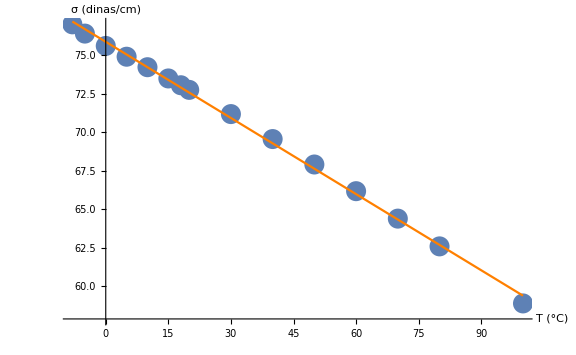

```mathematica
grafico1b = Plot[ajuste,{t,-8,100},PlotStyle->Orange,Evaluate[optam]];
Show[grafico1a,grafico1b]
```

## 3.

```mathematica
optam={ImageSize->Large,LabelStyle->Large};
```

Primeiramente vamos escrever ambas equações de movimento da forma:

```mathematica
edox = m *x''[t]+k*x[t]/(Sqrt[x[t]^2+y[t]^2]^(1+β))==0;
```

```mathematica
edoy =  m *y''[t]+k*y[t]/(Sqrt[x[t]^2+y[t]^2]^(1+β))==0;
```

```mathematica
subsex3 = {m ->20,k ->5000, a ->100,β->2}; (*Valores a serem susbtituídos para β = 2*)
```

Agora vamos resolver as equações diferenciais para as condições iniciais fornecidas. Note que a velocidade inicial em y foi derivada igualando-se a força central que temos com a força centrípeta (m*v^2/r^2) e isolando o v. Temos então:

```mathematica
solsex3 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^2)]}/.subsex3,{x[t],y[t]},{t,0,10000}] //First;
```

```mathematica
posx3[t_]:= x[t] /. solsex3[[1]]
posy3[t_]:= y[t] /. solsex3[[2]]
```

Agora vamos plotar as soluções em um plot paramétrico.

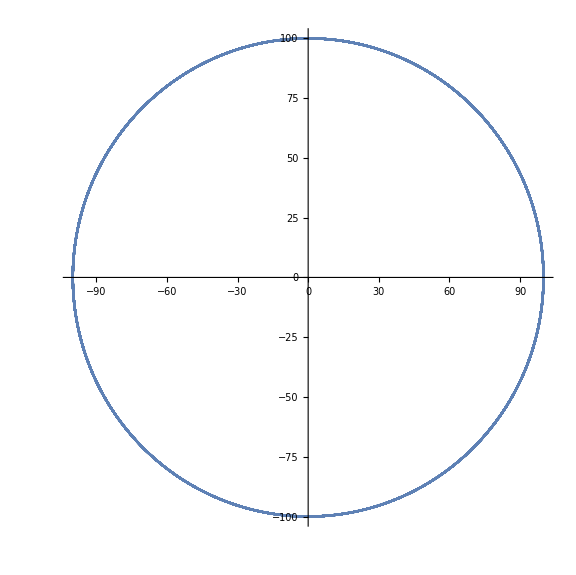

```mathematica
ParametricPlot[{posx3[t],posy3[t]},{t,0,10000}, Evaluate[optam]]
```

Como podemos ver, o resultado é exatamente o que esperávamos, que seria uma órbita circular. Agora vamos analisar mais 4 casos, aumentado a velocidade em 20% e depois em 30% , e também diminuindo a velocidade nas mesmas proporções, para  assim ver como a órbita se comporta.

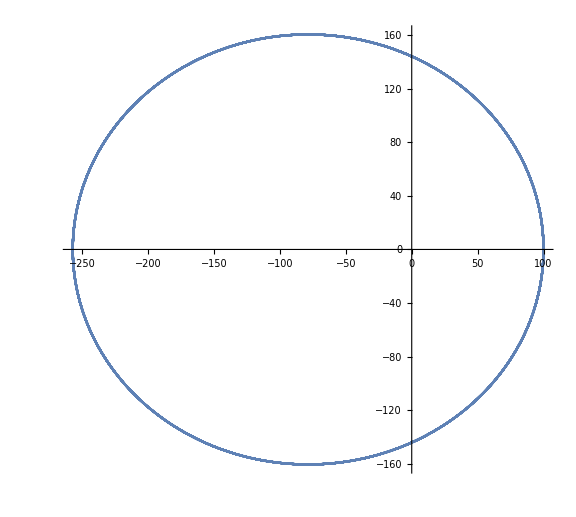

```mathematica
solsex31 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== 1.2*Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^2)]}/.subsex3,{x[t],y[t]},{t,0,10000}] //First;
posx31[t_]:= x[t] /. solsex31[[1]]
posy31[t_]:= y[t] /. solsex31[[2]]
ParametricPlot[{posx31[t],posy31[t]},{t,0,10000},Evaluate[optam]]
```

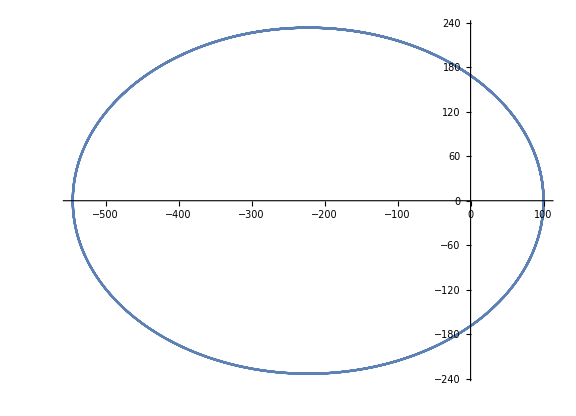

```mathematica
solsex32 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== 1.3*Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^2)]}/.subsex3,{x[t],y[t]},{t,0,10000}] //First;
posx32[t_]:= x[t] /. solsex32[[1]]
posy32[t_]:= y[t] /. solsex32[[2]]
ParametricPlot[{posx32[t],posy32[t]},{t,0,10000},Evaluate[optam]]
```

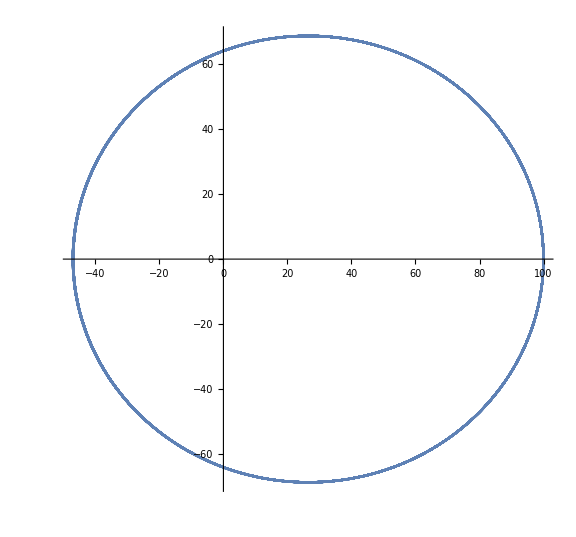

```mathematica
solsex33 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== 0.8*Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^2)]}/.subsex3,{x[t],y[t]},{t,0,10000}] //First;
posx33[t_]:= x[t] /. solsex33[[1]]
posy33[t_]:= y[t] /. solsex33[[2]]
ParametricPlot[{posx33[t],posy33[t]},{t,0,10000},Evaluate[optam]]
```

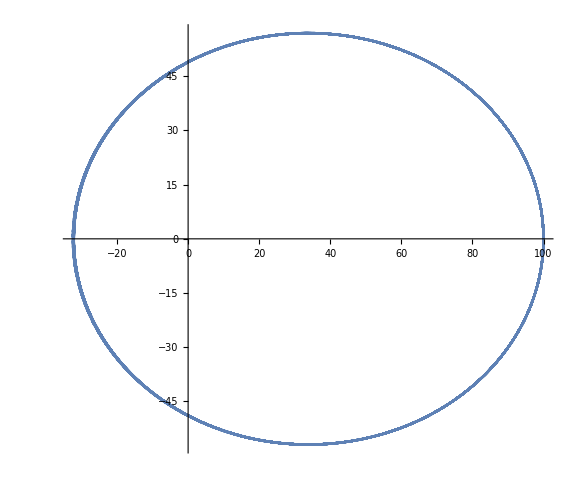

```mathematica
solsex34 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== 0.7*Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^2)]}/.subsex3,{x[t],y[t]},{t,0,10000}] //First;
posx34[t_]:= x[t] /. solsex34[[1]]
posy34[t_]:= y[t] /. solsex34[[2]]
ParametricPlot[{posx34[t],posy34[t]},{t,0,10000},Evaluate[optam]]
```

Podemos ver que em todos os casos foram produzidas órbitas elípticas (fechadas), como era de se esperar.

Agora vamos analisar um novo caso para quando β = 3, ou seja, para quando a força central cai com distância mais rápido que a gravidade.

Repare que agora temos um novo valor definido para velocidade inicial, que foi obtido exatamente pelo mesmo método utilizado no exemplo anterior. Finalmente, temos então:

```mathematica
subsbeta3 = {m ->20,k ->5000, a ->100,β->3}; (*novos valores para substituição*)
```

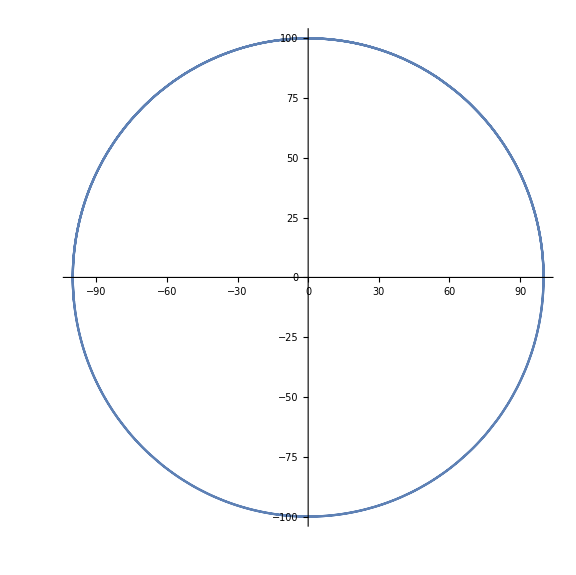

```mathematica
solsbeta3 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^3)]}/.subsbeta3,{x[t],y[t]},{t,0,10000}] //First;
posxnew[t_]:= x[t] /. solsbeta3[[1]]
posynew[t_]:= y[t] /. solsbeta3[[2]]
ParametricPlot[{posxnew[t],posynew[t]},{t,0,10000},Evaluate[optam]]
```

Vemos que a órbita é circular, pois escolhemos um valor de velocidade inicial que incidia neste comportamento. Agora vamos mudar apenas um pouco a velocidade inicial (20%) para ver como a trajetória vai se comportar:

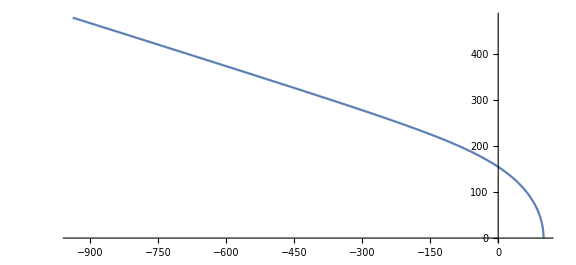

```mathematica
solsbeta31 = NDSolve[{edox,edoy,x[0] == a,y[0]==0,x'[0]==0,y'[0]== 1.2*Sqrt[k*a/(m*Sqrt[x[0]^2+y[0]^2]^3)]}/.subsbeta3,{x[t],y[t]},{t,0,10000}] //First;
posxnew1[t_]:= x[t] /. solsbeta31[[1]]
posynew1[t_]:= y[t] /. solsbeta31[[2]]
ParametricPlot[{posxnew1[t],posynew1[t]},{t,0,10000},Evaluate[optam]]
```

Vemos que, para uma força que decai com o cubo da distância, ao se alterar o valor da velocidade inicial, nós não temos mais uma órbita estável, agora a órbita é aberta (hiperbólica). Podemos imaginar como um corpo que passa por um planeta e depois desvia sua trajetória e continua seu caminho.